```mathematica
Clear[J,w2,F2,fw]
Print["John Window"]
w2[t_]:=a +b Cos[π t]+c Cos[2 π t]

f2[t_]:=Piecewise[{{w2[t], Abs[t]≤1}, {0, True}}]

Print["Fourier Transforming"]
F2=FourierTransform[f2[t],t,ω];
Jt[ω_,a_,b_,c_]=F2/Limit[F2,ω->0] //FullSimplify
Hn[ω_]=F[ω,1/2,1/2];
Hm[ω_]=F[ω,.54,.46];
```

John Window

Fourier Transforming

((4 a π^4-(5 a-4 b+c) π^2 ω^2+(a-b+c) ω^4) Sin[ω])/(a ω (4 π^4-5 π^2 ω^2+ω^4))

Setting Params

0.18

0.5

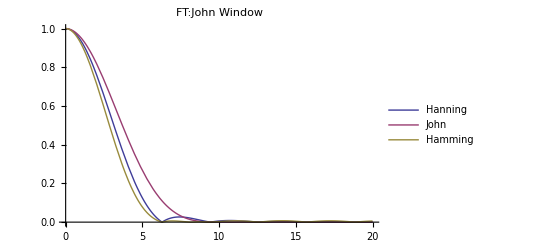

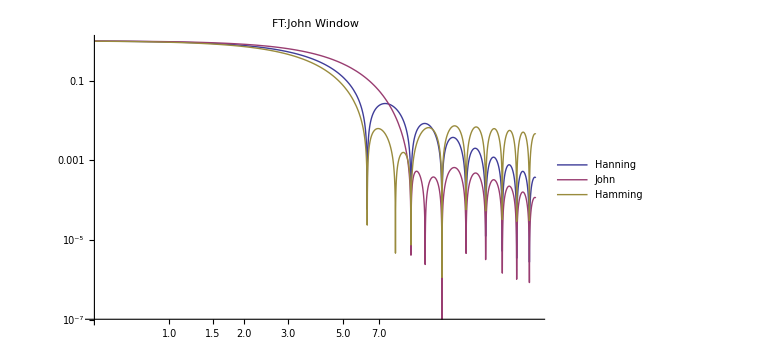

Solving for Max

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.000532592

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FWHM=0.880231

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

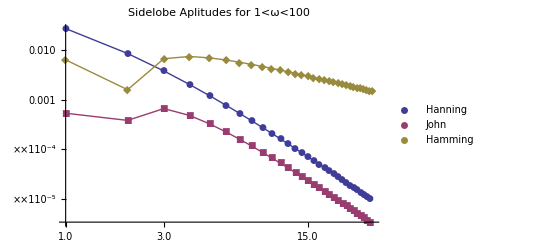

```mathematica
Print["Setting Params"]
α=.18
β=.50
(*Manipulate[*)
J[ω_]=Jt[ω,(1-β)(1-α),β,(1-β)α];
Plot[{Abs[ Hn[ω]], Abs[J[ω]], Abs[Hm[ω]]},{ω,0,20},PlotRange->All,PlotLabel->"FT:John Window",PlotLegends->{"Hanning","John","Hamming"}]
LogLogPlot[{Abs[Hn[ω]],Abs[J[ω]],Abs[Hm[ω]]},{ω,.5,30},PlotRange->All,PlotLabel->"FT:John Window",PlotLegends->{"Hanning","John","Hamming"},ImageSize->Large]
(**)Print["Solving for Max"];
solj=Solve[{D[J[ω],ω]==0,5<ω<20},ω][[1]];
Abs[J[ω]]/.solj
(*Print["FWHMing"];*)
fw=ω/.Solve[{J[ω]==J[ω/.solj]/2,5<ω<20},ω];
Print["FWHM=",fw[[2]]-fw[[1]]];
(*Print["More Plotting"];*)
ListLogLogPlot[{Abs[Hn[ω/.Solve[{D[Hn[ω],ω]==0,1<ω<100},ω]]],Abs[J[ω/.Solve[{D[J[ω],ω]==0,1<ω<100},ω]]],Abs[Hm[ω/.Solve[{D[Hm[ω],ω]==0,1<ω<100},ω]]]},PlotRange->All,PlotRange->All,PlotLegends->{"Hanning","John","Hamming"},Joined->True,PlotMarkers->Automatic,PlotLabel->"Sidelobe Aplitudes for 1<ω<100"](*,{α,0,.45,.01}]*)
```